Exercises for Section 8 | Basic Graphics Objects

Use RegularPolygon to draw a triangle. |

EXPECTED OUTPUT »

-Graphics- | ×



```mathematica
Graphics[RegularPolygon[3]]
```

Make graphics of a red circle. |

EXPECTED OUTPUT »

-Graphics- | ×

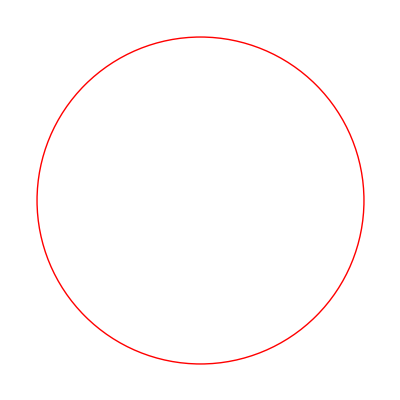



```mathematica
Graphics[{Red,Circle[]}]
Graphics[Style[Circle[],Red]]
```

Make a red octagon. |

EXPECTED OUTPUT »

-Graphics- | ×

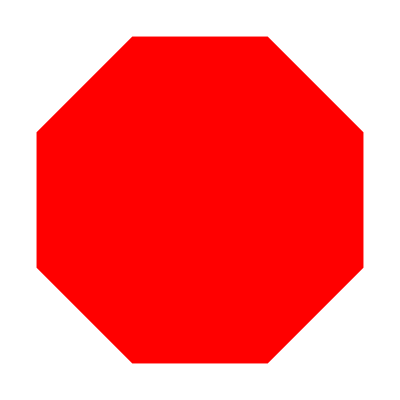

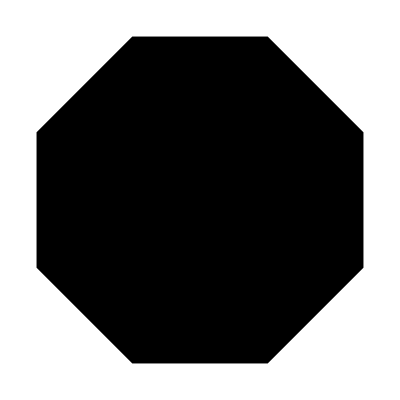

```mathematica
Graphics[{Red,RegularPolygon[8]}]
Graphics[Style[RegularPolygon[8],Red]]
```

Make a list whose elements are disks with hues varying from 0 to 1 in steps of 0.1. |

EXPECTED OUTPUT »

-Graphics- | ×


{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[Style[Disk[],Hue[x]]],{x,0,1,0.1}]
```

Make a column of a red and a green triangle. |

EXPECTED OUTPUT »

-Graphics- | ×

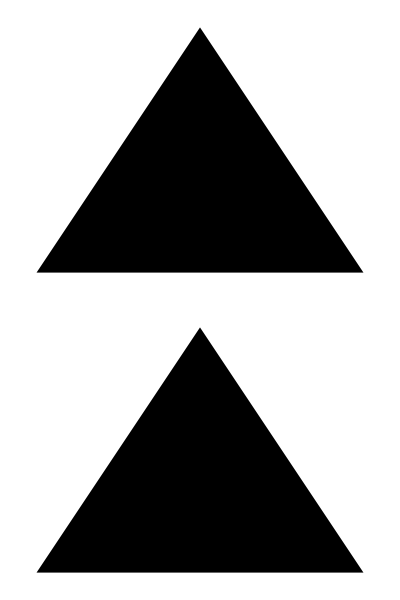

```mathematica
Column[{Graphics[Style[RegularPolygon[3],Red]],Graphics[Style[RegularPolygon[3],Green]]}]
```

Make a list giving the regular polygons with 5 through 10 sides, with each polygon being colored pink. |

EXPECTED OUTPUT »

-Graphics- | ×

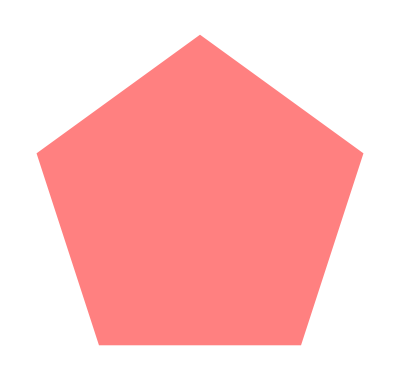
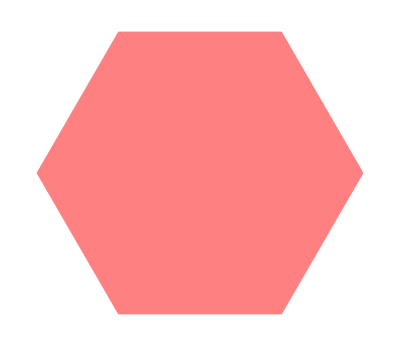
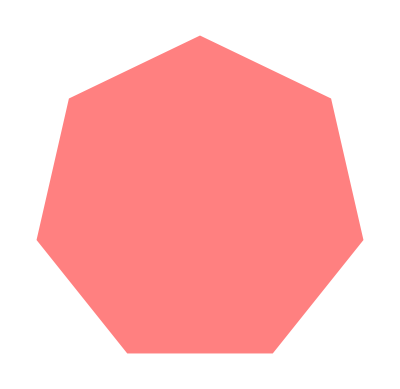
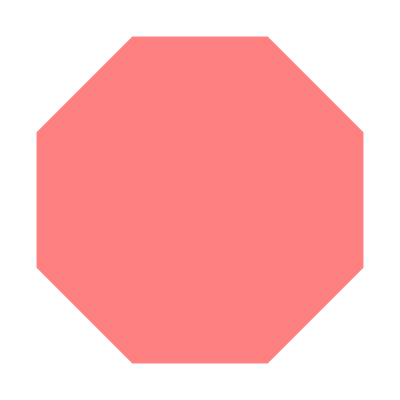
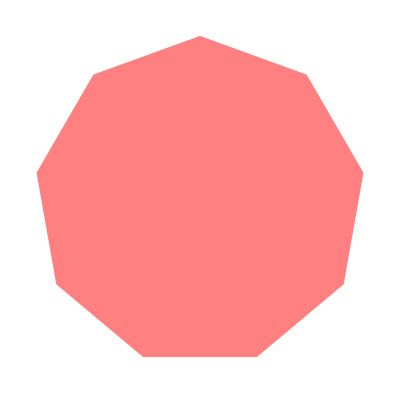
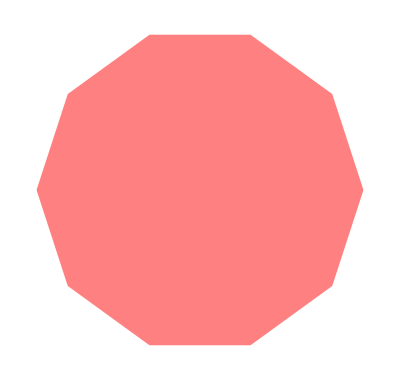

```mathematica
Table[Graphics[{Pink,RegularPolygon[numside]}],{numside,5,10}]
```

Make a graphic of a purple cylinder. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Graphics3D[Style[Cylinder[],Purple]]
```

-Graphics3D-

Make a list of polygons with 8, 7, 6, ... , 3 sides, and colored with RandomColor, then show them all overlaid with the triangle on top (hint: apply Graphics to the list). |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

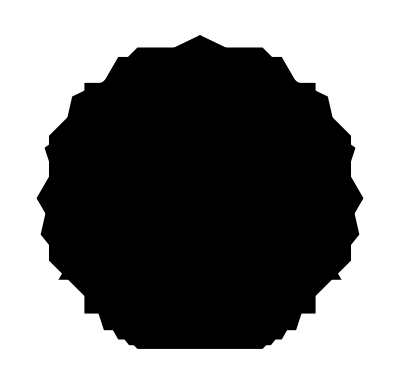

```mathematica
Graphics[Table[Style[RegularPolygon[numside],RandomColor[]],{numside,8,3,-1}]]
```

Make a list of 10 regular pentagons with random colors.  |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

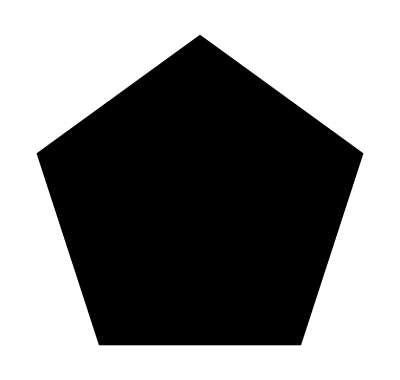
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[Style[RegularPolygon[5],RandomColor[]]],{10}]
```

Make a list of a 20-sided regular polygon and a disk. |

EXPECTED OUTPUT »

-Graphics- | ×

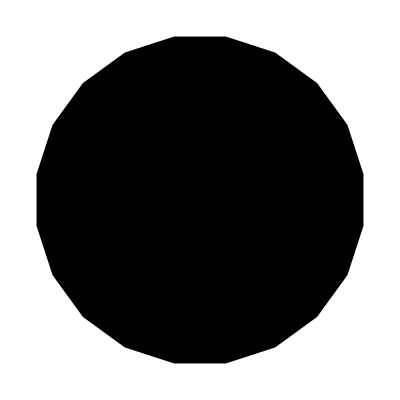
{-Graphics-,-Graphics-}

```mathematica
{Graphics[RegularPolygon[20]],Graphics[Disk[]]}
```

Make a list of polygons with 10, 9, ... , 3 sides. |

EXPECTED OUTPUT »

-Graphics- | ×

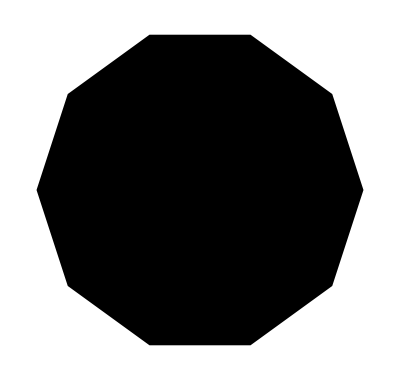
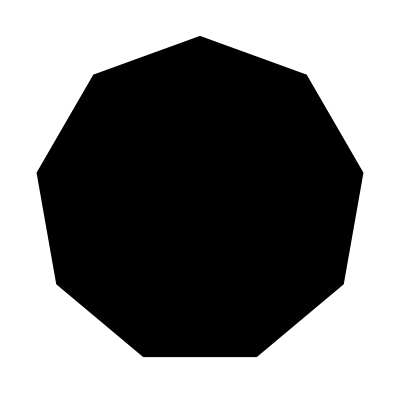
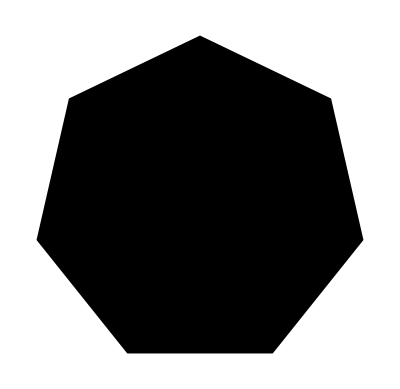
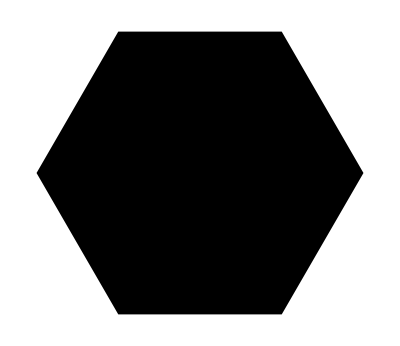

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[RegularPolygon[numsides]],{numsides,10,3,-1}]
```